# 2 D Square lattice with 2 atoms and p_(x,y) & d_(x^2-y^2) orbitals

Ángel Salazar 
School of Physical Sciences and Nanotechnology

Here we compute the associated Hamiltonian and the band structure.

-Graphics-

Let’s enter the Hamiltonian’s elements

```mathematica
h[1,1]=ep +4  tpp Cos[a/(√2) kx] Cos[a/(√2)ky];
h[2,2]=ep +4  tpp Cos[a/(√2) kx] Cos[a/(√2)ky];
h[3,3]=ed +4  tdd Cos[a/(√2) kx] Cos[a/(√2)ky];
h[1,2]=h[2,1]=0;
h[1,3]=tpd (1-Exp[-ⅈ √2 a kx]);
h[3,1]=tpd(1-Exp[ⅈ √2 a kx]);
h[2,3]=-2 ⅈ tpd Exp[(-ⅈ a kx)/(√2)] Sin[(a ky)/(√2)];
h[3,2]=+2 ⅈ tpd Exp[(ⅈ a kx)/(√2) ]Sin[(a ky)/(√2)];
```

```mathematica
H=Table[h[i,j],{i,3},{j,3}];
H//MatrixForm
```

(ep+4 tpp Cos[(a kx)/(√2)] Cos[(a ky)/(√2)] | 0 | (1-ⅇ^(-ⅈ √2 a kx)) tpd
0 | ep+4 tpp Cos[(a kx)/(√2)] Cos[(a ky)/(√2)] | -2 ⅈ ⅇ^(-(ⅈ a kx)/(√2)) tpd Sin[(a ky)/(√2)]
(1-ⅇ^(ⅈ √2 a kx)) tpd | 2 ⅈ ⅇ^((ⅈ a kx)/(√2)) tpd Sin[(a ky)/(√2)] | ed+4 tdd Cos[(a kx)/(√2)] Cos[(a ky)/(√2)])

```mathematica
eigenv=(Eigenvalues[H]//FullSimplify)//PowerExpand;
```

```mathematica
eigenv
```

{ep+4 tpp Cos[(a kx)/(√2)] Cos[(a ky)/(√2)],1/2 ⅇ^(-ⅈ √2 a kx) (ⅇ^(ⅈ √2 a kx) (ed+ep)+2 ⅇ^((ⅈ a kx)/(√2)) (1+ⅇ^(ⅈ √2 a kx)) (tdd+tpp) Cos[(a ky)/(√2)]-ⅇ^(ⅈ √2 a kx) √((ed-ep)^2+4 (4 tpd^2+(tdd-tpp)^2)+4 (-2 tpd^2+(tdd-tpp)^2) Cos[√2 a kx]+8 (ed-ep) (tdd-tpp) Cos[(a kx)/(√2)] Cos[(a ky)/(√2)]+8 (-tpd^2+(tdd-tpp)^2 Cos[(a kx)/(√2)]^2) Cos[√2 a ky])),1/2 ⅇ^(-ⅈ √2 a kx) (ⅇ^(ⅈ √2 a kx) (ed+ep)+2 ⅇ^((ⅈ a kx)/(√2)) (1+ⅇ^(ⅈ √2 a kx)) (tdd+tpp) Cos[(a ky)/(√2)]+ⅇ^(ⅈ √2 a kx) √((ed-ep)^2+4 (4 tpd^2+(tdd-tpp)^2)+4 (-2 tpd^2+(tdd-tpp)^2) Cos[√2 a kx]+8 (ed-ep) (tdd-tpp) Cos[(a kx)/(√2)] Cos[(a ky)/(√2)]+8 (-tpd^2+(tdd-tpp)^2 Cos[(a kx)/(√2)]^2) Cos[√2 a ky]))}

Here the lattice vectors

```mathematica
a1=a/(√2){1,-1,0};
a2 = a/(√2){1,1,0};
a3 = {0,0,1};
b1= (2 π a2×a3)/(a1.(a2×a3))
b2= (2 π a3×a1)/(a1.(a2×a3))
```

{(√2 π)/a,-(√2 π)/a,0}

{(√2 π)/a,(√2 π)/a,0}

```mathematica
Plot3D[Table[eigenv[[i]],{i,3}]/.{ep->-2,ed->-1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π}//Evaluate,{kx,-1.3,1.3},{ky,-1.3,1.3},
MaxRecursion->3,
PlotPoints->40,
BoxRatios->{1, 1, 1},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞}

]
```

-Graphics3D-

Let' s visualize the band structure within the IBZLet' s visualize the band structure within the IBZ

```mathematica
Plot3D[Table[eigenv[[i]],{i,3}]/.{ep->-2,ed->-1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π}//Evaluate,{kx,-1.3,1.3},{ky,-1.3,1.3},
MaxRecursion->3,
PlotPoints->40,
BoxRatios->{1, 1, 1},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞},
RegionFunction->Function[{x,y,z},y<x&&x≥0 && y≥0]
]
```

-Graphics3D-

Now let’ manipulate this BS;

```mathematica
Manipulate[Plot3D[Table[eigenv[[i]],{i,3}]/.{ep->epval,ed->edval,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π}//Evaluate,{kx,-1.3,1.3},{ky,-1.3,1.3},
MaxRecursion->3,
PlotPoints->40,
BoxRatios->{1, 1, 1},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞},
RegionFunction->Function[{x,y,z},y<x&&x≥0 && y≥0]

],
{{epval,-1.5,"ϵ_p"},-2,-0.5},{{edval,0.5,"ϵ_d"},0.1,1.5}
]
```

For some regions we can get the dirac cone ()

Remember the relationship of energy and momentum ,the energy is proportional to the momentum, E= ℏkc.  The electron is behaving as a massless particle in a Dirac Cone.

### BANDS1

Let' s  compute the BS along the high symmetry points Γ-M-X-Γ.

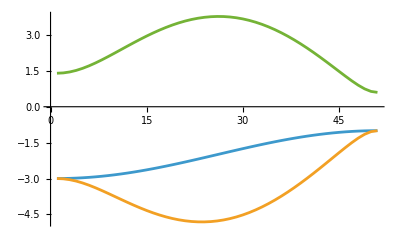

```mathematica
Table[ΓM[i]=Table[eigenv[[i]]/.{ep->-2,ed->1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π,ky->0},{kx,0,1,0.02}


],{i,3}];

pathΓM=ListPlot[Table[ΓM[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+0,#1}&,#]&,{i,3}],
Joined->True,
PlotRange->All

]
```

now  along the path M to X

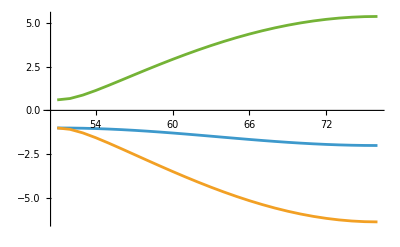

```mathematica
Table[MX[i]=Table[eigenv[[i]]/.{ep->-2,ed->1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π,ky->kx-1},{kx,1,0.5,-0.02}


],{i,3}];

pathMX=ListPlot[Table[MX[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+50,#1}&,#]&,{i,3}],
Joined->True,
PlotRange->All

]
```

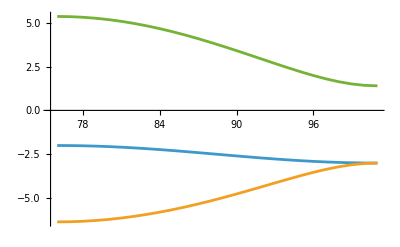

```mathematica
Table[XΓ[i]=Table[eigenv[[i]]/.{ep->-2,ed->1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π,ky->-kx},{kx,0.5,0,-0.02}


],{i,3}];

pathXΓ=ListPlot[Table[XΓ[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+75,#1}&,#]&,{i,3}],
Joined->True,
PlotRange->All]
```

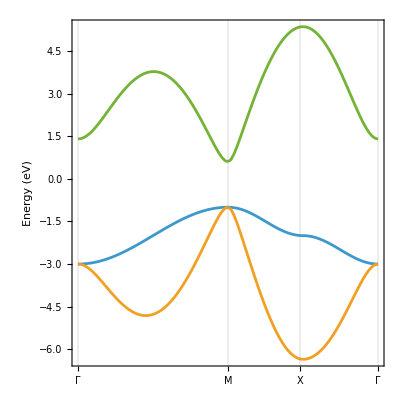

```mathematica
gridline={1,51,75,101};
hsplabel={"Γ","M","X","Γ"};
Show[pathΓM,pathMX,pathXΓ,
PlotRange->All,
Frame->True,
FrameLabel->{"","Energy (eV)"},
Axis->None,
AspectRatio->1,
GridLines->{gridline,None},
FrameTicks->{{Automatic,None},{{gridline,hsplabel}//Transpose,None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15}
]
```

### 3D

Let’s check the dirac cones

```mathematica
Plot3D[{eigenv[[2]],eigenv[[3]]}/.{ep->-0.8,ed->0.5,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π}//Evaluate,{kx,-1.3,1.3},{ky,-1.3,1.3},
MaxRecursion->3,
PlotPoints->40,
BoxRatios->{1, 1, 1},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞}

]
```

-Graphics3D-

### BANDS2

Let' s  compute the BS along the high symmetry points Γ-M-X-Γ.

```mathematica
Table[ΓM[i]=Table[eigenv[[i]]/.{ep->-2,ed->1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π,ky->0},{kx,0,1,0.02}


],{i,3}];

pathΓM=ListPlot[Table[ΓM[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+0,#1}&,#]&,{i,3}],
Joined->True,
PlotRange->All

]
```

-Graphics-

now  along the path M to X

```mathematica
Table[MX[i]=Table[eigenv[[i]]/.{ep->-2,ed->1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π,ky->kx-1},{kx,1,0.5,-0.02}


],{i,3}];

pathMX=ListPlot[Table[MX[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+50,#1}&,#]&,{i,3}],
Joined->True,
PlotRange->All

]
```

-Graphics-

```mathematica
Table[XΓ[i]=Table[eigenv[[i]]/.{ep->-2,ed->1,tpp->-0.25,tdd->0.1,tpd->2,a->√2 π,ky->-kx},{kx,0.5,0,-0.02}


],{i,3}];

pathXΓ=ListPlot[Table[XΓ[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+75,#1}&,#]&,{i,3}],
Joined->True,
PlotRange->All]
```

-Graphics-

```mathematica
gridline={1,51,75,101};
hsplabel={"Γ","M","X","Γ"};
Show[pathΓM,pathMX,pathXΓ,
PlotRange->All,
Frame->True,
FrameLabel->{"","Energy (eV)"},
Axis->None,
AspectRatio->1,
GridLines->{gridline,None},
FrameTicks->{{Automatic,None},{{gridline,hsplabel}//Transpose,None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15}
]
```

-Graphics-